ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[{{0, 5}}, <>][t]

1.

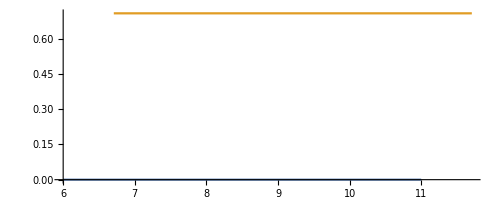

```mathematica
ClearAll["Global`*"]

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];


xsol=ListInterpolation[{6,11},{0,5}][t]
j0=g[xsol,0,Pi/4];
j1=j0.g[1,0,0];

ghandball=Inverse[ghand].gball; (* ball in wrist frame *)
j01=Inverse[j0].j1;

N[j01[[1,3]]/.t->1]

coordj0[t_]:={j0[[1,3]],j0[[2,3]]};
coordj1[t_]:={j1[[1,3]],j1[[2,3]]};

ParametricPlot[{coordj0[t],coordj1[t]},{t,0,5}]
```